# IoT Connectivity and the Wolfram Blockchain

by Tony Koop
Mentor - Matthew Szudzik
with special help from Jesse Friedman

The World Meteorological Organization has over 11,000 weather stations around the world. The data from these devices are continuously recorded into public databases and made available for anyone to download and analyze. Meteorologists regularly inform their viewers with reports produced by Weather, Research & Forecast (WRF) models which analyze these aggregated datasets. In addition to the WMO’s stations, there are also civilian owned weather stations that inform platforms like Weather Underground, AcuRite, and Weather Bug. Unfortunately, those companies do not share the profits they generate off the data they collect from the community. Also, AcuRite no longer offers a public API for their users to easily access their own data. Even worse, WeatherBug has been caught selling private location data about their users to third parties.

Concerns for privacy and data ownership are on the rise. Though Facebook experienced moderate backlash for its role in the Cambridge Analytica scandal, many opine the reaction was insufficient. Switching costs remain high while data produced by users remains hosted the platform’s servers.  One way to deal with this is to backup your own data in a secondary location such that it’s available for personal use any time.

Insert your own myAcuRite login credentials into the code below and then evaluate the cell to obtain a table of the latest reading from your personal weather station. After the code retrieves the current data feed, it will be inserted into the Wolfram Blockchain and a public databin which can be accessed at the URL below. If the data is successfully inserted into the blockchain and recalled without changing the data, “True” will appear above the weather table.

Databin: wolfr.am/EM6FHeXi

```mathematica
(*Send a login request with username and password to get a session token and account ID*)
loginData=URLExecute[HTTPRequest[<|
Method->"POST",
"Scheme"->"https",
"Domain"->"marapi.myacurite.com",
"Path"->"/users/login",
"ContentType"->"application/json",
"Body"->ExportString[<|

"email"->"wrfcoin@gmx.com",
"password"->"h5h3f**kD",

"remember"->"True"
|>,"RawJSON"]|>],"RawJSON"];

(*Find the ID of the particular weather station in question*)
hubsData=URLExecute[HTTPRequest[<|
   Method -> "GET",
   "Scheme" -> "https",
   "Domain" -> "marapi.myacurite.com/accounts/"<>ToString[loginData[["user","account_users",1,"account_id"]]]<>"/dashboard/hubs",
   "ContentType"->"application/json",
   "Headers" -> {"x-one-vue-token" -> loginData["token_id"]}|>],"RawJSON"];
 myhubid=hubsData[["account_hubs",1,"id"]];
 
 (*Otain the current data feed from the particular weather station*)
 weatherfeed=URLExecute[HTTPRequest[<|
   Method -> "GET",
   "Scheme" -> "https",
   "Domain" -> "marapi.myacurite.com/accounts/"<>ToString[loginData[["user","account_users",1,"account_id"]]]<>"/dashboard/hubs/"<>ToString[myhubid],
   "ContentType"->"application/json",
   "Headers" -> {"x-one-vue-token" -> loginData["token_id"]}|>],"RawJSON"];
   
   (*Organize data. Consider cases with different units*)
   deviceRawData=weatherfeed[["devices",1]];
   sensorRawData=AssociationThread[deviceRawData[["sensors",All,"sensor_name"]]->deviceRawData[["sensors"]]];
   sensorUnits=<|
   "Temperature"->Switch[sensorRawData["Temperature","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Pressure"->Switch[sensorRawData["Pressure","chart_unit"],"inHg","InchesOfMercury","hPa","Hectopascals"],
   "Humidity"->"Percent",
   "Wind Speed"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"],
   "Wind Direction"->"Degrees",
   "Rainfall"->Switch[sensorRawData["Rainfall","chart_unit"],"in","Inches","mm","Millimeters"],
   "Dew Point"->Switch[sensorRawData["Dew Point","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Feels Like"->Switch[sensorRawData["Feels Like","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Wind Speed Average"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"]|>;
	
sensorData=<|"Sensor"->#["sensor_name"],"Value"->Quantity[#["last_reading_value"],sensorUnits[#["sensor_name"]]]|>&/@Values@sensorRawData;

(*Include timestamp, latitude, longitude, and elevation into the table*)
isoStringWithTZToDateObject[string_String]:=
(* by Jesse *)Module[{stringParts=StringSplit[string,RegularExpression["(?=((\\+|-)\\d{2}:\\d{2})|Z$)"]],tzpart,tzoffset,signedtzoffset},
Which[Length[stringParts]===1,signedtzoffset=Automatic,ToUpperCase[stringParts[[2]]]==="Z",signedtzoffset=0,True,tzpart=StringSplit[stringParts[[2]],
{RegularExpression["(?<=\\+|-)"],":"}];
tzoffset=NumberCompose[FromDigits/@Rest[tzpart],{1,1/60}];
signedtzoffset=N@If[tzpart[[1]]==="-",-tzoffset,tzoffset];];
DateObject[stringParts[[1]],TimeZone->signedtzoffset]]

weatherEntry=dataTable=<|
"Sensors"->sensorData,
"Timestamp"->TimeZoneConvert[isoStringWithTZToDateObject[deviceRawData["last_check_in_at"]]],
"Position"->GeoPosition[Append[
Interpreter["Real"][{weatherfeed["latitude"],weatherfeed["longitude"]}],
Quantity[weatherfeed["elevation"],Switch[weatherfeed["elevation_unit"],"ft","Feet","m","Meters"]]]]|>;

convertWeatherEntryToCompleteSet[weatherEntry_]:= Module[
	{sensorData, time, geolocation, sensorIndex = 1, timeIndex = 2, positionIndex = 3},	
	sensorData = Values /@ Values[weatherEntry]⟦sensorIndex⟧;
	time = "Timestamp" -> Values[weatherEntry]⟦timeIndex⟧;
	geolocation = "Position" -> Values[weatherEntry]⟦positionIndex⟧;	
	Association @ Flatten @ Join[{time, geolocation, Rule @@@ sensorData}]]

(*Insert the weatherEntry and its hash into the Wolfram Blockchain and a Databin*)
previousHash=Hash[Normal[Databin["EM6FHeXi",-1]][[1,2]],"SHA256"];
list={previousHash, weatherEntry};
trxID=BlockchainPut[list];
listDB={previousHash, Hash[weatherEntry,"SHA256"],trxID};
DatabinAdd["EM6FHeXi",listDB];

(*Check that the entry returned from the blockchain computes the same weatherHash, recall last ten entries into Databin*)
Hash[BlockchainGet[trxID]⟦2⟧, "SHA256"]===Hash[weatherEntry, "SHA256"]
convertWeatherEntryToCompleteSet[weatherEntry]//Dataset
```

True

Dataset[<>]

# Weather Station Density

Data deserts in the field of meteorology exist in places like northern Canada, inland China, and North Africa. One of the largest factors contributing to weather forecasting inaccuracy is a lack of data from these areas.  A typical World Meteorological Organization weather station costs several thousand dollars for a government to install. Deciding where to install new weather stations depends on a several factors such as weather patterns, population centers, budgets, and accessibility. Though local governments may not have the budget to install an official WMO station, it is still important to collect data generated from local denizens.

Use the cell below to import the dataset of WMO stations for the United States, Canada and Mexico. After that, calculate the average distance to the nearest weather station by plotting 100 random points in each country and determine the average distance to the nearest WMO Station. As can be seen, the United States has the highest density of weather station while Canada has a lower density than Mexico.

```mathematica
WMOStations=ResourceObject["WMO Meteorological Stations"];
WMOLocations=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="United States"&], "Position"];
pts=RandomGeoPosition[Entity["Country","UnitedStates"],200];
GeoGraphics[{{Red,Point/@WMOLocations},{Black,Point[pts]}},GeoRange->Entity["Country","UnitedStates"]]
nearestDistances = GeoNearest[WMOLocations//Normal,pts[[1]]];
Print["Average Distance to nearest WMO Station"]
Mean[GeoDistance@@@Transpose[{nearestDistances[[All,1,1]],pts[[1]]}]]
Print["WMO Stations per Square Mile"]
ScientificForm[Length[WMOLocations]/EntityValue[Entity["Country","UnitedStates"],"Area"]]

WMOLocationsCA=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="Canada"&], "Position"];
ptsCA=RandomGeoPosition[LinguisticAssistant,200];
GeoGraphics[{{Red,Point/@WMOLocationsCA},{Black,Point[ptsCA]}},GeoRange->LinguisticAssistant]
nearestDistancesCA = GeoNearest[WMOLocationsCA//Normal,ptsCA[[1]]];
Print["Average Distance to nearest WMO Station"]
Mean[GeoDistance@@@Transpose[{nearestDistancesCA[[All,1,1]],ptsCA[[1]]}]]
Print["WMO Stations per Square Mile"]
ScientificForm[Length[WMOLocationsCA]/EntityValue[Entity["Country","Canada"],"Area"]]

WMOLocationsMX=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="Mexico"&], "Position"];
ptsMX=RandomGeoPosition[Entity["Country","Mexico"],200];
GeoGraphics[{{Red,Point/@WMOLocationsMX},{Black,Point[ptsMX]}},GeoRange->Entity["Country","Mexico"]]
nearestDistancesMX = GeoNearest[WMOLocationsMX//Normal,ptsMX[[1]]];
Print["Average Distance to nearest WMO Station"]
Mean[GeoDistance@@@Transpose[{nearestDistancesMX[[All,1,1]],ptsMX[[1]]}]]
Print["WMO Stations per Square Mile"]
ScientificForm[Length[WMOLocationsMX]/EntityValue[Entity["Country","Mexico"],"Area"]]
```

-Graphics-

Average Distance to nearest WMO Station

47.6369 mi

WMO Stations per Square Mile

1.52741×10^-4 per mile^2

-Graphics-

Average Distance to nearest WMO Station

68.5858 mi

WMO Stations per Square Mile

1.46818×10^-4 per mile^2

$Aborted

Average Distance to nearest WMO Station

65.4709 mi

WMO Stations per Square Mile

1.08115×10^-4 per mile^2

```mathematica
(*WMOLocationsRA=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="Russia"&], "Position"];
ptsRA=RandomGeoPosition[Entity["Country","Russia"],100];
GeoGraphics[{{Red,Point/@WMOLocationsRA},{Black,Point[ptsRA]}},GeoRange->Entity["Country","Russia"]]
nearestDistancesRA = GeoNearest[WMOLocationsRA//Normal,ptsRA[[1]]];
Print["Average Distance to nearest WMO Station"]
Mean[GeoDistance@@@Transpose[{nearestDistancesRA[[All,1,1]],ptsRA[[1]]}]]
Print["WMO Stations per Square Mile"]
ScientificForm[Length[WMOLocationsRA]/EntityValue[Entity["Country","Russia"],"Area"]]*)

WMOLocationsAL=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="Algeria"&], "Position"];
ptsAL=RandomGeoPosition[Entity["Country","Algeria"],100];
GeoGraphics[{{Red,Point/@WMOLocationsAL},{Black,Point[ptsAL]}},GeoRange->Entity["Country","Algeria"]]
nearestDistancesAL = GeoNearest[WMOLocationsAL//Normal,ptsAL[[1]]];
Print["Average Distance to nearest WMO Station"]
Mean[GeoDistance@@@Transpose[{nearestDistancesAL[[All,1,1]],ptsAL[[1]]}]]
Print["WMO Stations per Square Mile"]
ScientificForm[Length[WMOLocationsAL]/EntityValue[Entity["Country","Algeria"],"Area"]]

(*WMOLocationsFR=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="France"&], "Position"];
ptsFR=RandomGeoPosition[Entity["Country","France"],100];
GeoGraphics[{{Red,Point/@WMOLocationsFR},{Black,Point[ptsFR]}},GeoRange->Entity["Country","France"]]
nearestDistancesFR = GeoNearest[WMOLocationsFR//Normal,ptsFR[[1]]];
Print["Average Distance to nearest WMO Station"]
Mean[GeoDistance@@@Transpose[{nearestDistancesFR[[All,1,1]],ptsFR[[1]]}]]
Print["WMO Stations per Square Mile"]
ScientificForm[Length[WMOLocationsFR]/EntityValue[Entity["Country","France"],"Area"]]*)
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

RandomGeoPosition::invloc: Missing[RetrievalFailure] is not a valid location specification.

-Graphics-

Average Distance to nearest WMO Station

Transpose::nmtx: The first two levels of {{32.3333,35.1667,35.2667,35.0667,35.1667,35.1,35.2333,35.1833,35.1833,35.1,35.1,35.0833,35.4,35.2833,35.3,35.25,35.2833,35.5333,35.5,«14»,34.3,34.3333,34.45,34.6667,34.5167,34.5833,34.75,34.5167,34.1333,34.2333,34.3667,34.2667,34.4,34.8,34.75,34.8333,34.6667,«30»},«1»} cannot be transposed.

GeoDistance::invloc: 32.3333 is not a valid location specification.

GeoDistance::invloc: 35.1667 is not a valid location specification.

GeoDistance::invloc: 35.2667 is not a valid location specification.

General::stop: Further output of GeoDistance::invloc will be suppressed during this calculation.

Mean[Transpose[GeoDistance[{32.3333,35.1667,35.2667,35.0667,35.1667,35.1,35.2333,35.1833,35.1833,35.1,35.1,35.0833,35.4,35.2833,35.3,35.25,35.2833,35.5333,35.5,35.5,35.6167,35.7167,34.1167,35.7167,35.7833,35.7,35.7333,35.9333,35.8167,34.1833,34.2,34.1167,34.1167,34.3,34.3333,34.45,34.6667,34.5167,34.5833,34.75,34.5167,34.1333,34.2333,34.3667,34.2667,34.4,34.8,34.75,34.8333,34.6667,34.9,34.7,34.8167,33.1833,33.2,34.9833,33.1333,33.3167,33.1333,33.85,32.2333,33.0667,35.1167,32.8833,32.7333,32.5,31.2333,31.6167,30.3833,30.0833,30.3333,29.4333,29.8667,28.75,27.95,26.1167,26.8,25.5,23.45,21.2167},Entity[Country,Algeria]]]]

WMO Stations per Square Mile

EntityValue::nodat: Unable to download data. Some or all results may be missing.

83/Missing[RetrievalFailure]

# Proximity to Neighbors

One way to determine where the next weather station should be installed is to calculate the  a 

Use the cell below to import the dataset of WMO stations for the United States, Canada and Mexico. After that, calculate the average distance to the nearest weather station by plotting 100 random points in each country and determine the average distance to the nearest WMO Station. As can be seen, the United States has the highest density of weather station while Canada has a lower density than Mexico.

```mathematica
(*Display a map showing the location of the weather station*)
(*Given the location of WMO weather stations, calculate radius to cirumscribe 50 WMO stations.*)


(*GeoGraphics[{{Red,Point/@WMOLocationsMX},{Black,Point[ptsMX]}},GeoRange->Entity["Country","Mexico"]]*)

GeoGraphics[GeoDisk[ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 
		GeoRange-> GeoDistanceList[GeoNearest[Normal[WMOLocations], 
		ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 20]]//Max]]
		
GeoListPlot[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 20]]	


(*Find the closest WMO weather station and compare the data from your weather station. 
Take 100 random locations across the US and calculate the average "proximity value" for those areas*)

loc=GeoPosition[ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}];

list={
Mean[GeoDistance[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]},1], loc]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 10]]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 50]]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 100]]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 200]]]}
```

-Graphics-

-Graphics-

{42.443 mi,75.8268 mi,163.894 mi,220.845 mi,350.57 mi}

# Data Charting & Visualization

Compare the data feed from the weather station to the nearest official weather station which is KBED located at the

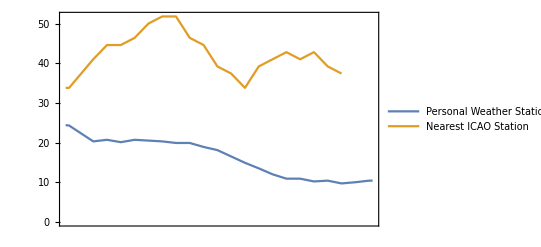

```mathematica
(*Collect recent Blockchain sumbissions from the weather station and chart the temperature over time*)  
Databin["EM6FHeXi", All];
recentHashes=Normal[Dataset[Databin["EM6FHeXi", -24]]][[All,1,-1]];
data=Dataset[BlockchainGet[recentHashes]];
times=data[[1;;All,2,2]]//Normal;
temps=data[[1;;All,2,1,1,2]]//Normal;
myTempsTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@temps}]];
wmoTempsTimeSeries=TimeSeries[Transpose[{times, AirTemperatureData["KBED", times]}]];
DateListPlot[{myTempsTimeSeries,wmoTempsTimeSeries}, 
	PlotLegends->{"Personal Weather Station","Nearest ICAO Station"}]
```

```mathematica
(*Chart the weather station's Humidity*)
humidity=data[[1;;All,2,1,2,2]]//Normal;
myHumidityTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@humidity}]];
wmoHumidityTimeSeries=WeatherData["KBED","Humidity",{Now-Quantity[1, "Days"], Now}]*100;
DateListPlot[{myHumidityTimeSeries,wmoHumidityTimeSeries},
	PlotLegends->{"Personal Weather Station","Nearest ICAO Station"}]
```

Part::partd: Part specification Dataset[$Failed]⟦1;;All,2,1,2,2⟧ is longer than depth of object.

Dataset`ExtractRawData::dataextr: Data extraction failed.

Part::pkspec1: The expression MapAt[ToExpression,2,1] cannot be used as a part specification.

Transpose::nmtx: The first two levels of {Dataset[$Failed]⟦1;;All,2,2⟧,Dataset[$Failed]⟦1;;All,MapAt[ToExpression,2,1],MapAt[ToExpression,1,1],MapAt[ToExpression,2,1],MapAt[ToExpression,2,1]⟧} cannot be transposed.

DateListPlot::ldata: … is not a valid dataset or list of datasets.

DateListPlot[{TimeSeries[Transpose[{Dataset[$Failed]⟦1;;All,2,2⟧,Dataset[$Failed]⟦1;;All,MapAt[ToExpression,2,1],MapAt[ToExpression,1,1],MapAt[ToExpression,2,1],MapAt[ToExpression,2,1]⟧}]],TimeSeries[…]},PlotLegends→{Personal Weather Station,Nearest ICAO Station}]

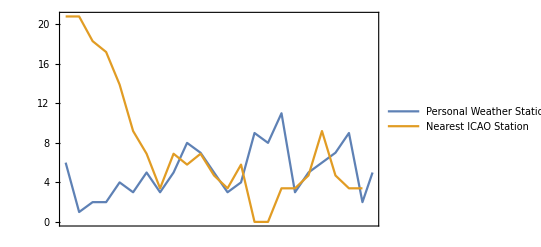

```mathematica
(*Chart the weather station's Wind Speed*)
windSpeed=data[[1;;All,2,1,3,2]]//Normal;
myWindTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@windSpeed}]];
wmoWindTimeSeries=TimeSeries[Transpose[{times, WindSpeedData["KBED", times]}]];
DateListPlot[{myWindTimeSeries, wmoWindTimeSeries},
	PlotLegends->{"Personal Weather Station","Nearest ICAO Station"}]
```

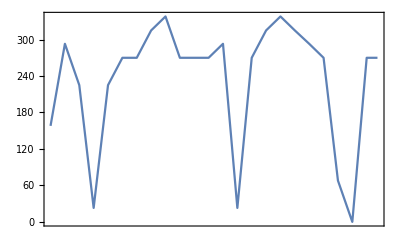

0. °

```mathematica
(*Chart the weather station's Wind Direction*)
windDirection=data[[1;;All,2,1,4,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@windDirection}]]
WindDirectionData["KBED", Now]
```

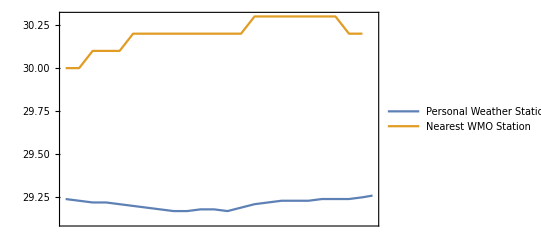

```mathematica
(*Chart the weather station's Pressure*)
pressure=data[[1;;All,2,1,7,2]]//Normal;

myPressureTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@pressure}]];
wmoPressureTimeSeries=TimeSeries[Transpose[{times, AirPressureData["KBED", times]}]];
DateListPlot[{myPressureTimeSeries,wmoPressureTimeSeries}, PlotLegends->{"Personal Weather Station","Nearest WMO Station"}]
```

# Cloud Deploy Scheduled Task

The first cell of this notebook automatically inputs the current weather data from a personal weather station into the Wolfram Blockchain and a Databin. Use the cell below to have this task executed once per hour using CloudDeploy and ScheduledTask. Enter your own MyAcuRite email and password along with the name of your own Databin.

```mathematica
isoStringWithTZToDateObject[string_String]:=
(* by Jesse *)Module[{stringParts=StringSplit[string,RegularExpression["(?=((\\+|-)\\d{2}:\\d{2})|Z$)"]],tzpart,tzoffset,signedtzoffset},Which[Length[stringParts]===1,signedtzoffset=Automatic,ToUpperCase[stringParts[[2]]]==="Z",signedtzoffset=0,True,tzpart=StringSplit[stringParts[[2]],{RegularExpression["(?<=\\+|-)"],":"}];
tzoffset=NumberCompose[FromDigits/@Rest[tzpart],{1,1/60}];
signedtzoffset=N@If[tzpart[[1]]==="-",-tzoffset,tzoffset];];
DateObject[stringParts[[1]],TimeZone->signedtzoffset]];
(*frequency=Quantity[15, "Minutes"];*)
frequency=Quantity[60, "Minutes"];
stask=ScheduledTask[Module[{
loginData,
mytoken,
myaccountid,
hubsData,
myhubid,
weatherfeed,
deviceRawData,
sensorRawData,
sensorUnits,
sensorData,
weatherEntry,
weatherHash,
list,
trxID
},
(*Send a login request with username and password to get a session token and account ID*)
loginData=URLExecute[HTTPRequest[<|
Method->"POST",
"Scheme"->"https",
"Domain"->"marapi.myacurite.com",
"Path"->"/users/login",
"ContentType"->"application/json",
"Body"->ExportString[
<|
"email"->"wrfcoin@gmx.com",
"password"->"h5h3f**kD",
"remember"->"True"
|>,
"RawJSON"]
|>],"RawJSON"];

mytoken=loginData["token_id"];
myaccountid=loginData[["user","account_users",1,"account_id"]];

(*Find the ID of the particular weather station in question*)
hubsData=URLExecute[HTTPRequest[<|
 Method -> "GET",
"Scheme" -> "https",
"Domain" -> "marapi.myacurite.com/accounts/"<>ToString[myaccountid]<>"/dashboard/hubs","ContentType"->"application/json",
"Headers" -> {"x-one-vue-token" -> mytoken}
|>],"RawJSON"];
 myhubid=hubsData[["account_hubs",1,"id"]];

(*Obtain the current data feed from the particular weather station*)
weatherfeed=URLExecute[HTTPRequest[<|
Method -> "GET",
"Scheme" -> "https",
"Domain" -> "marapi.myacurite.com/accounts/"<>ToString[myaccountid]<>"/dashboard/hubs/"<>ToString[myhubid],
"ContentType"->"application/json",
"Headers" -> {"x-one-vue-token" -> mytoken}
|>],"RawJSON"];

(*Organize data. Consider cases with different units*)
deviceRawData=weatherfeed[["devices",1]];
sensorRawData=AssociationThread[deviceRawData[["sensors",All,"sensor_name"]]->deviceRawData[["sensors"]]];
sensorUnits=<|
"Temperature"->Switch[sensorRawData["Temperature","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
"Pressure"->Switch[sensorRawData["Pressure","chart_unit"],"inHg","InchesOfMercury","hPa","Hectopascals"],
"Humidity"->"Percent",
"Wind Speed"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"],"Wind Direction"->"Degrees",
"Rainfall"->Switch[sensorRawData["Rainfall","chart_unit"],"in","Inches","mm","Millimeters"],
"Dew Point"->Switch[sensorRawData["Dew Point","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
"Feels Like"->Switch[sensorRawData["Feels Like","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
"Wind Speed Average"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"]
|>;
sensorData=<|"Sensor"->#["sensor_name"],"Value"->Quantity[#["last_reading_value"],sensorUnits[#["sensor_name"]]]|>&/@Values@sensorRawData;


(*Include timestamp, latitude, longitude, and elevation into the table*)

weatherEntry=dataTable=<|
"Sensors"->sensorData,
"ReadingTimestamp"->TimeZoneConvert[isoStringWithTZToDateObject[deviceRawData["last_check_in_at"]]],
"SubmisisonTimestamp"->Now,
"Position"->GeoPosition[Append[
Interpreter["Real"][{weatherfeed["latitude"],weatherfeed["longitude"]}],
Quantity[weatherfeed["elevation"],Switch[weatherfeed["elevation_unit"],"ft","Feet","m","Meters"]]]]
|>;

(*Insert the weatherEntry and its hash into the Wolfram Blockchain and a Databin*)
previousHash=Hash[Normal[Databin["EM6FHeXi",-1]][[1,2]],"SHA256"];
list={previousHash, weatherEntry};
trxID=BlockchainPut[list];
listDB={previousHash, Hash[weatherEntry,"SHA256"],trxID};
DatabinAdd["EM6FHeXi",listDB];
],frequency];
task=SessionSubmit[Evaluate@stask];

obj=CloudDeploy[stask,"BlockchainWeatherUpdate"]
```

CloudObject[https://www.wolframcloud.com/obj/user-09a7a86c-3b31-48b5-8722-6b255f3bede3/BlockchainWeatherUpdate]